```mathematica
q[w_]:=(w-1/2)
```

```mathematica
h[w_]:=-l v q[w]q'[w]
```

```mathematica
g[w_]:=l{-v q[w]q'[w],Sqrt[v/2]q'[w]}/Sqrt[b]
```

```mathematica
D1[w_]:=h[w]+g[w].g'[w]
```

```mathematica
D2[w_]:=g[w].g[w]
```

```mathematica
FullSimplify[D2[w],Assumptions->{v>0,l>0}]
```

(l^2 v (2+v (1-2 w)^2))/(4 b)

```mathematica
FullSimplify[-D1[w]+D2'[w],Assumptions->{v>0,l>0}]
```

(l v (b+l v) (-1+2 w))/(2 b)

```mathematica
(*singular*)
```

```mathematica
q[w_]:=(w-1)^2
```

```mathematica
h[w_]:=-l v q[w]q'[w]
```

```mathematica
g[w_]:=l{-v q[w]q'[w],Sqrt[v/2]q'[w]}/Sqrt[b]
```

```mathematica
D1[w_]:=h[w]+g[w].g'[w]
```

```mathematica
D2[w_]:=g[w].g[w]
```

```mathematica
FullSimplify[D2[w],Assumptions->{v>0,l>0}]
```

(2 l^2 v (1+2 v (-1+w)^4) (-1+w)^2)/b

```mathematica
FullSimplify[-D1[w]+D2'[w],Assumptions->{v>0,l>0}]
```

(2 l v (l (1+6 v (-1+w)^4)+b (-1+w)^2) (-1+w))/b

```mathematica
k[x_,y_]:=(x)^2(x^2+y^2)^2;
```

```mathematica
n=10;
Plot3D[Exp[-n k[x,y]],{x,-1,2},{y,-1,1}]
```

-Graphics3D-

```mathematica
Clear[x,y]
```

```mathematica
q[x_,y_]:=x(x^2+y^2);
grad[x_,y_]:=Evaluate@{D[q[x,y],x],D[q[x,y],y]}
```

```mathematica
grad[x,y]
```

{3 x^2+y^2,2 x y}

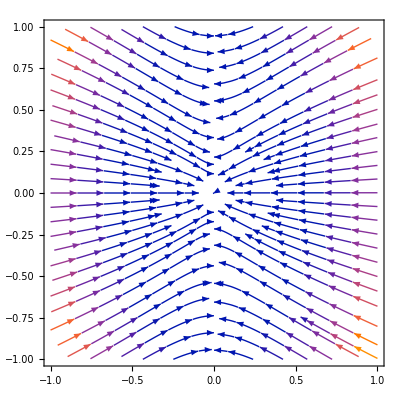

```mathematica
(* Negative gradient of the model *)
Block[{vxy=0,vxx=1},StreamPlot[-(vxx q[x,y]-vxy)grad[x,y],{x,-1,1},{y,-1,1}]]
```

```mathematica
(* Product of derivatives *)
Table[D[q[x,y],i]D[q[x,y],j],{i,{x,y}},{j,{x,y}}]
```

{{(3 x^2+y^2)^2,2 x y (3 x^2+y^2)},{2 x y (3 x^2+y^2),4 x^2 y^2}}

```mathematica
(* covariance matrix *)
Σ[x_,y_]:=γ^2(σv^2 q[x,y]+σc^2){{(3 x^2+y^2)^2,2 x y (3 x^2+y^2)},{2 x y (3 x^2+y^2),4 x^2 y^2}}
```

```mathematica
(* average values *)
μ[x_,y_]:=-γ s^2 q[x,y] grad[x,y]
```

```mathematica
Eigensystem[Σ[x,y]]
```

{{0,(9 x^4+10 x^2 y^2+y^4) γ^2 (σc^2+x^3 σv^2+x y^2 σv^2)},{{-(2 x y)/(3 x^2+y^2),1},{-(-3 x^2-y^2)/(2 x y),1}}}

```mathematica
grad[x,y]
```

{3 x^2+y^2,2 x y}

```mathematica
(* 1d version *)
```

```mathematica
q[w_]:=(w-1)w^2;
gradq[w_]:=w^2+2w(w-1);
μ[w_]:=-γ s^2 q[w] gradq[w];
Var[w_]:=γ^2(σv^2 q[w]+σc^2)gradq[w]^2;
```

```mathematica
RateProb[w_,w0_]:=PDF[NormalDistribution[μ[w0],Sqrt[Var[w0]]],w]
```

```mathematica
Block[{γ=1,s=1,σv=1,σc=1},
a=Integrate[(w1-w)RateProb[w1,w],{w1,-Infinity,Infinity}];
Print[a]]
```

ConditionalExpression[-(w (1+(-1+w) w^2 (-2+3 w)))/(√π √(1/((2-3 w)^2 w^2 (π+π (-1+w) w^2))) √((2-3 w)^2 w^2 (1-w^2+w^3))), Re[1/((2-3 w)^2 w^2 (1-w^2+w^3))]≥0]

```mathematica
Block[{γ=1,s=1,σv=1,σc=1},
b=Integrate[(w1-w)^2 RateProb[w1,w],{w1,-Infinity,Infinity}];
Print[b]]
```

ConditionalExpression[(w^2 (5+w (-12+w (9+(-1+w) w (-2+3 w) (3+(-1+w) w (-2+3 w))))))/(√π √(1/((2-3 w)^2 w^2 (π+π (-1+w) w^2))) √((2-3 w)^2 w^2 (1-w^2+w^3))), Re[1/((2-3 w)^2 w^2 (1-w^2+w^3))]≥0]

```mathematica
Simplify[-(w (1+(-1+w) w^2 (-2+3 w)))/(√π √(1/((2-3 w)^2 w^2 (π+π (-1+w) w^2))) √((2-3 w)^2 w^2 (1-w^2+w^3))),Assumptions->{-.2<=w<=1.2}]
```

-w (1+2 w^2-5 w^3+3 w^4)

```mathematica
Simplify[(w^2 (5+w (-12+w (9+(-1+w) w (-2+3 w) (3+(-1+w) w (-2+3 w))))))/(√π √(1/((2-3 w)^2 w^2 (π+π (-1+w) w^2))) √((2-3 w)^2 w^2 (1-w^2+w^3))),Assumptions->{-.2<=w<=1.2}]
```

w^2 (5-12 w+9 w^2+6 w^3-11 w^4-11 w^5+37 w^6-30 w^7+9 w^8)

```mathematica
D[w^2 P[w],{w,2}]
```

2 P[w]+4 w P'[w]+w^2 P''[w]

```mathematica
D[w P[w],w]
```

P[w]+w P'[w]

```mathematica
DSolve[P[w]+w P'[w]+5(2 P[w]+4 w P'[w]+w^2 P''[w])==0,P[w],w]
```

{{P[w]→C[1]/w^(11/5)+C[2]/w}}

```mathematica
bb=w^2 (5-12 w+9 w^2+6 w^3-11 w^4-11 w^5+37 w^6-30 w^7+9 w^8);
aa=-w (1+2 w^2-5 w^3+3 w^4);
```

```mathematica
DSolve[D[bb P[w],{w,2}]-D[aa P[w],w]==0,P[w],w]
```

{{P[w]→[w]}}

```mathematica
NDSolve[{D[bb P[w],{w,2}]-D[aa P[w],w]==0,P[10]==1,P'[10]==1},P[w],{w,.01,10}]
```

{{P[w]→InterpolatingFunction[…][w]}}

```mathematica
Q[w_]:=w^2;
```

{1.02689,{w→-0.208376}}

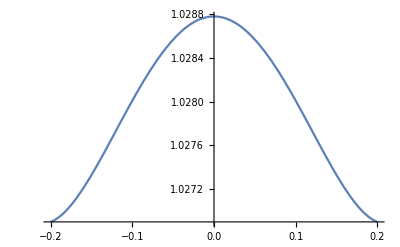

```mathematica
n=100;
y=RandomVariate[NormalDistribution[0,1],n];
x=RandomVariate[NormalDistribution[0,1],n];
Minimize[Mean[(y-Q[w]x)^2],w]
Plot[Mean[(y-Q[w]x)^2],{w,-.2,.2}]
```

```mathematica
min[n_]:=Block[{w,x,y},
y=RandomVariate[NormalDistribution[0,1],n];
x=RandomVariate[NormalDistribution[0,1],n];
Return[w/.Minimize[Mean[(y-Q[w]x)^2],w][[2]]]]
```

```mathematica
nsamp=10^4;
mins=Table[min[10],nsamp];
```

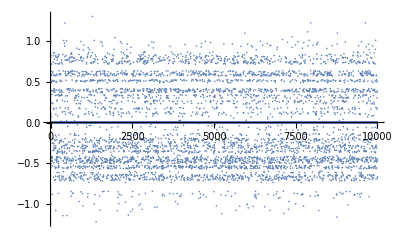

```mathematica
ListPlot[mins]
```

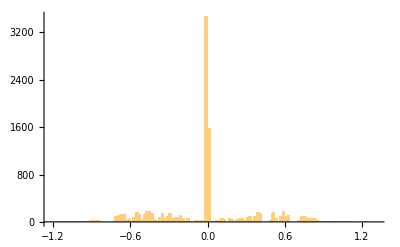

```mathematica
Histogram[mins,100]
```